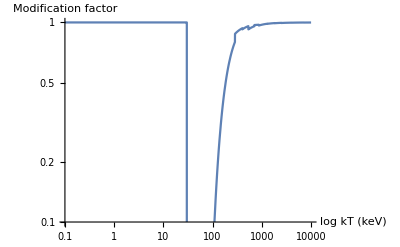

```mathematica
(*Поглощение на водороде*)

Clear["Global`*"]
c0[x_]:=Piecewise[{
{17.3,0.030<x<0.100},
	{34.6,0.100<x<0.284},
	{78.1,0.284<x<0.400},
{71.4,0.400<x<0.532},
	{95.5,0.532<x<0.707},
	{308.9,0.707<x<0.867},
	{120.6,0.867<x<1.303},
	{141.3,1.303<x<1.840},
	{202.7,1.840<x<2.471},
	{342.7,2.471<x<3.210},
	{352.2,3.210<x<4.038},
	{433.9,4.038<x<7.111},
	{629.0,7.111<x<8.331},
	{701.2,8.331<x<10.000}},0];

c1[x_]:=Piecewise[{
{608.1,0.030<x<0.100},
	{267.9,0.100<x<0.284},
	{18.8,0.284<x<0.400},
{66.8,0.400<x<0.532},
	{145.8,0.532<x<0.707},
	{-380.6,0.707<x<0.867},
	{169.3,0.867<x<1.303},
	{146.8,1.303<x<1.840},
	{104.7,1.840<x<2.471},
	{18.7,2.471<x<3.210},
	{18.7,3.210<x<4.038},
	{-2.4,4.038<x<7.111},
	{30.9,7.111<x<8.331},
	{25.2,8.331<x<10.000}},0];

c2[x_]:=Piecewise[{
{-2150.,0.030<x<0.100},
	{-476.1,0.100<x<0.284},
	{4.3,0.284<x<0.400},
{-51.4,0.400<x<0.532},
	{-61.1,0.532<x<0.707},
	{294.0,0.707<x<0.867},
	{-47.7,0.867<x<1.303},
	{-31.5,1.303<x<1.840},
	{-17.0,1.840<x<2.471},
	{0.0,2.471<x<3.210},
	{0.0,3.210<x<4.038},
	{0.75,4.038<x<7.111},
	{0.0,7.111<x<8.331},
	{0.0,8.331<x<10.000}},0];

sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=10.9*10^(19);
extinctionCurve[x_]:=Exp[-sigma[x]*Nh];
LogLogPlot[Exp[-sigma[x/1000]*Nh],{x,10^(-1),10^4}, AxesLabel->{"log kT (keV)","Modification factor"} ,PlotRange->{{All,All},{0.1,1.}}]
```

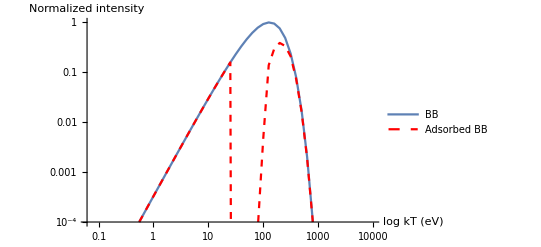

```mathematica
Clear["Global`*"]

(*Температура*)
T:=46;


(*Спектр ЧТ*)
Planck[w_]:=w^3/(4 Pi^3)/(Exp[w/T]-1);

(*Импорт данных*)
energyLogValues=Range[-1,4,0.1];
energyValues = 10^x/.x->energyLogValues;

(*Расчет спектра ЧТ*)
planckValues := Planck[energyValues]/Max[ Planck[energyValues]];

(*Коэффициенты кривой поглощения*)
c0[x_]:=Piecewise[{
{17.3,0.030<x<=0.100},
	{34.6,0.100<=x<0.284},
	{78.1,0.284<=x<0.400},
{71.4,0.400<=x<0.532},
	{95.5,0.532<=x<0.707},
	{308.9,0.707<=x<0.867},
	{120.6,0.867<=x<1.303},
	{141.3,1.303<=x<1.840},
	{202.7,1.840<=x<2.471},
	{342.7,2.471<=x<3.210},
	{352.2,3.210<=x<4.038},
	{433.9,4.038<=x<7.111},
	{629.0,7.111<=x<8.331},
	{701.2,8.331<=x<10.000}},0];
c1[x_]:=Piecewise[{
{608.1,0.030<x<=0.100},
	{267.9,0.100<=x<0.284},
	{18.8,0.284<=x<0.400},
{66.8,0.400<=x<0.532},
	{145.8,0.532<=x<0.707},
	{-380.6,0.707<=x<0.867},
	{169.3,0.867<=x<1.303},
	{146.8,1.303<=x<1.840},
	{104.7,1.840<=x<2.471},
	{18.7,2.471<=x<3.210},
	{18.7,3.210<=x<4.038},
	{-2.4,4.038<=x<7.111},
	{30.9,7.111<=x<8.331},
	{25.2,8.331<=x<10.000}},0];
c2[x_]:=Piecewise[{
{-2150.,0.030<x<=0.100},
	{-476.1,0.100<=x<0.284},
	{4.3,0.284<=x<0.400},
{-51.4,0.400<=x<0.532},
	{-61.1,0.532<=x<0.707},
	{294.0,0.707<=x<0.867},
	{-47.7,0.867<=x<1.303},
	{-31.5,1.303<=x<1.840},
	{-17.0,1.840<=x<2.471},
	{0.0,2.471<=x<3.210},
	{0.0,3.210<=x<4.038},
	{0.75,4.038<=x<7.111},
	{0.0,7.111<=x<8.331},
	{0.0,8.331<=x<10.000}},0];

(*Сигма, кол-во атомов водорода *)
sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=12.9*10^(19);

(*Кривая поглощения, переводим энергию в keV*)
extinctionCurve[energyEv_]:=Exp[-sigma[energyEv*0.001]*Nh];

(*Modification factor для поглощения*)
adsorbtionValues:=extinctionCurve/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValues=Planck[energyValues]*adsorbtionValues/Max[Planck[energyValues]];

(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixed = ListLogLogPlot[Transpose[{energyValues, planckValues}],
PlotRange->{{All,All},{0.0001,1}},PlotLegends->{"BB" },Joined->True];

plotMixed =  ListLogLogPlot[Transpose[{energyValues, adsorbedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{All,All},{0.0001,1}},PlotLegends->{"Adsorbed BB" },Joined->True];

Show[plotUnmixed,plotMixed, AxesLabel->{"log kT (eV)","Normalized intensity"} ]
```

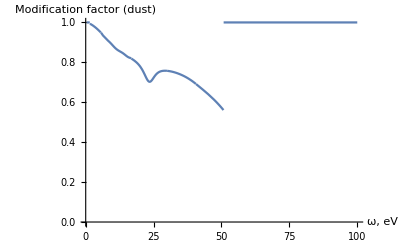

```mathematica
(*Поглощение на пыли*)

(*Коэффициенты кривой поглощения*)

Fa[x_]:=Piecewise[ {{-0.04473(x-5.9)^2-0.009779(x-5.9)^3, 5.9≤x≤8}},
0];
Fb[x_]:=Piecewise[ {{0.2130(x-5.9)^2+0.1207(x-5.9)^3, 5.9≤x≤8}},
0];

a[x_]:=Piecewise[{
{0.574 x^(1.61),0.3<x≤1.1},
	{1+0.104*(x-1.82)-0.609*(x-1.82)^2+0.701*(x-1.82)^3+1.137*(x-1.82)^4-1.718*(x-1.82)^5-0.827*(x-1.82)^6+1.647*(x-1.82)^7-0.505*(x-1.82)^8,1.1<=x<3.3},
{1.752-0.316x-0.104/((x-4.67)^2+0.341)+Fa[x],3.3<=x<8},
{-1.073-0.628(x-8)+0.137(x-8)^2-0.070(x-8)^3,8≤x<10}},
	0];
b[x_]:=Piecewise[{
{-0.527  x^(1.61),0.3<x≤1.1},
	{1.952*(x-1.82)+2.908*(x-1.82)^2-3.989*(x-1.82)^3-7.985*(x-1.82)^4+11.102*(x-1.82)^5+5.491*(x-1.82)^6-10.805*(x-1.82)^7+3.347*(x-1.82)^8,1.1<=x<3.3},
{-3.090+1.825x+1.206/((x-4.62)^2+0.263)+Fb[x],3.3<=x<8},
{13.670+4.257(x-8)-0.420(x-8)^2+0.374(x-8)^3,8≤x<10}},
0];
Rv:=3.1;
Av:=0.12;
extinctionCurveDustMkMeters[mkM_]:=10^(-0.4*0.12*(a[mkM]+b[mkM]/Rv ));
extinctionCurveDustMkMeters1[mkM_]:=a[mkM]+b[mkM]/Rv;
extinctionCurveDustEv[eV_]:=extinctionCurveDustMkMeters[eV*0.197]
extinctionCurveDustAngst[Angst_]:=extinctionCurveDustMkMeters[1/(0.0001*Angst)]
Plot[extinctionCurveDustEv[x],{x,0.3,100},AxesLabel->{"ω, eV","Modification factor (dust)"},PlotRange->{{All,All},{0,1}}]
```

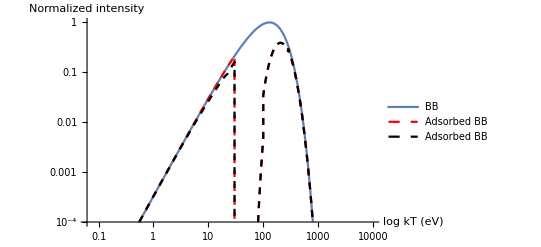

```mathematica
Clear["Global`*"]

(*Температура*)
T:=46;


(*Спектр ЧТ*)
Planck[w_]:=w^3/(4 Pi^3)/(Exp[w/T]-1);

(*Импорт данных*)
energyLogValues=Range[-1,4,0.001];
energyValues = 10^x/.x->energyLogValues;

(*Расчет спектра ЧТ*)
planckValues := Planck[energyValues]/Max[ Planck[energyValues]];

(*Коэффициенты кривой поглощения*)
c0[x_]:=Piecewise[{
{17.3,0.030<x<=0.100},
	{34.6,0.100<=x<0.284},
	{78.1,0.284<=x<0.400},
{71.4,0.400<=x<0.532},
	{95.5,0.532<=x<0.707},
	{308.9,0.707<=x<0.867},
	{120.6,0.867<=x<1.303},
	{141.3,1.303<=x<1.840},
	{202.7,1.840<=x<2.471},
	{342.7,2.471<=x<3.210},
	{352.2,3.210<=x<4.038},
	{433.9,4.038<=x<7.111},
	{629.0,7.111<=x<8.331},
	{701.2,8.331<=x<10.000}},0];
c1[x_]:=Piecewise[{
{608.1,0.030<x<=0.100},
	{267.9,0.100<=x<0.284},
	{18.8,0.284<=x<0.400},
{66.8,0.400<=x<0.532},
	{145.8,0.532<=x<0.707},
	{-380.6,0.707<=x<0.867},
	{169.3,0.867<=x<1.303},
	{146.8,1.303<=x<1.840},
	{104.7,1.840<=x<2.471},
	{18.7,2.471<=x<3.210},
	{18.7,3.210<=x<4.038},
	{-2.4,4.038<=x<7.111},
	{30.9,7.111<=x<8.331},
	{25.2,8.331<=x<10.000}},0];
c2[x_]:=Piecewise[{
{-2150.,0.030<x<=0.100},
	{-476.1,0.100<=x<0.284},
	{4.3,0.284<=x<0.400},
{-51.4,0.400<=x<0.532},
	{-61.1,0.532<=x<0.707},
	{294.0,0.707<=x<0.867},
	{-47.7,0.867<=x<1.303},
	{-31.5,1.303<=x<1.840},
	{-17.0,1.840<=x<2.471},
	{0.0,2.471<=x<3.210},
	{0.0,3.210<=x<4.038},
	{0.75,4.038<=x<7.111},
	{0.0,7.111<=x<8.331},
	{0.0,8.331<=x<10.000}},0];

(*Сигма, кол-во атомов водорода *)
sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=12.9*10^(19);

(*Кривая поглощения, переводим энергию в keV*)
extinctionCurve[energyEv_]:=Exp[-sigma[energyEv*0.001]*Nh];

(*Modification factor для поглощения*)
adsorbtionValues:=extinctionCurve/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValues=Planck[energyValues]*adsorbtionValues/Max[Planck[energyValues]];

(*Поглощение на пыли*)
(*Коэффициенты кривой поглощения*)

Fa[x_]:=Piecewise[ {{-0.04473(x-5.9)^2-0.009779(x-5.9)^3, 5.9≤x≤8}},
0];
Fb[x_]:=Piecewise[ {{0.2130(x-5.9)^2+0.1207(x-5.9)^3, 5.9≤x≤8}},
0];

a[x_]:=Piecewise[{
{0.574 x^(1.61),0.3<x≤1.1},
	{1+0.104*(x-1.82)-0.609*(x-1.82)^2+0.701*(x-1.82)^3+1.137*(x-1.82)^4-1.718*(x-1.82)^5-0.827*(x-1.82)^6+1.647*(x-1.82)^7-0.505*(x-1.82)^8,1.1<=x<3.3},
{1.752-0.316x-0.104/((x-4.67)^2+0.341)+Fa[x],3.3<=x<8},
{-1.073-0.628(x-8)+0.137(x-8)^2-0.070(x-8)^3,8≤x<10}},
	0];
b[x_]:=Piecewise[{
{-0.527  x^(1.61),0.3<x≤1.1},
	{1.952*(x-1.82)+2.908*(x-1.82)^2-3.989*(x-1.82)^3-7.985*(x-1.82)^4+11.102*(x-1.82)^5+5.491*(x-1.82)^6-10.805*(x-1.82)^7+3.347*(x-1.82)^8,1.1<=x<3.3},
{-3.090+1.825x+1.206/((x-4.62)^2+0.263)+Fb[x],3.3<=x<8},
{13.670+4.257(x-8)-0.420(x-8)^2+0.374(x-8)^3,8≤x<10}},
0];

Rv:=3.1;
extinctionCurveDustMkMeters[mkM_]:=10^(-0.4*0.12*(a[mkM]+b[mkM]/Rv));
extinctionCurveDustEv[eV_]:=extinctionCurveDustMkMeters[eV*0.197];

(*Modification factor для поглощения на пыли*)
adsorbtionValuesDust:=extinctionCurveDustEv/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValuesDust=adsorbedPlanckValues*adsorbtionValuesDust;



(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixed = ListLogLogPlot[Transpose[{energyValues, planckValues}],
PlotRange->{{All,All},{0.0001,1}},PlotLegends->{"BB" },Joined->True];

plotMixed =  ListLogLogPlot[Transpose[{energyValues, adsorbedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{All,All},{0.0001,1}},PlotLegends->{"Adsorbed BB" },Joined->True];

plotMixedDust =  ListLogLogPlot[Transpose[{energyValues, adsorbedPlanckValuesDust}],PlotStyle->{Black,Dashed},
PlotRange->{{All,All},{0.0001,1}},PlotLegends->{"Adsorbed BB" },Joined->True];


Show[plotUnmixed,plotMixed,plotMixedDust , AxesLabel->{"log kT (eV)","Normalized intensity"} ]
```

```mathematica
extinctionCurveDustEv[28.7]
```

0.0991078